# Effetto Tunnel

## Calcolo ed analisi di di Fourier

Appunti Meccanica Quantistica
  G. Paffuti

Vogliamo studiare numericamente l'effetto tunnel. Useremo come termine di confronto il caso esattamente risolubile di una barriera rettangolare, la procedura però vale in qualunque caso simile.

#### Strategia

Usiamo unità ℏ = m = 1. ene = k^2/2 ;

L'equazione da risolvere è

-1/2 ψ''[x] + V[x] ψ[x] = k^2/2 ψ[x]

Le soluzione si deve comprtare asintoticamente come

x << 0:    ψ ∼ Exp[ⅈ k x] + R Exp[-ⅈ k x];
x>> 0:   ψ ~ T Exp[ⅈ k x];

Siccome l' equazione è lineare dividiamo per T ed abbiamo il comportamento

x << 0:    ψ ∼1/T Exp[ⅈ k x] + R/T Exp[-ⅈ k x];
x>> 0:   ψ ~  Exp[ⅈ k x];

Quindi a grandi x, per un punto xR molto a destra

ψ[xR]=Exp[ⅈ k xR];   ψ'[xR]= ⅈ k Exp[ⅈ k x]

La strategia è quindi

Scegliamo un intervallo  [xL, xR] grande rispetto alla estensione del potenziale, e che contiene il potenziale

Risolviamo l’equazione differenziale (1) con la condizione al contorno (3). Otterremo a sinistra il valore di ψ e della sua derivata. Poniamo ψL = ψ[xL],   ξ =(1/i k) ψ’[L]/ψ[L].

Effettuando la derivata della formula asintotica (2) a sinistra si ricavano subito R e T in funzione di ψL e ξ:

R = (1-ξ)/(1+ξ)Exp[2ⅈ k xL];   T = 2/((1+ξ)ψL)Exp[ⅈ k xL]

La (4) risolve il problema.

In questo notebook si usa la funzione di Mathematica NDSolve che permette la soluzione numerica di un’equazione differenziale.

La funzione calcCoefficient[ene,V,xL,xR]  ha come input una lista di energie, il potenziale, gli estremi dell’intervallo. L’output sono aR, aT i due coefficienti di riflessione e trasmissione.

#### Funzioni per la soluzione del problema e per i controlli

```mathematica
calcCoefficient[ene_,V_,xL_,xR_]:=
Module[{k,ψL,ξ,aR,aT,sol,ris,y},
k = Flatten[{√(2ene)}];
 ris = Table[sol = NDSolve[{y''[x] + k[[j]]^2y[x] -2 V[x]y[x] ==0,
y[xR]== ⅇ^(ⅈ k[[j]] xR),y'[xR]==ⅈ k[[j]] ⅇ^(ⅈ k[[j]] xR)},y,{x,xR,xL}];
{y[xL],y'[xL]/(ⅈ k[[j]] y[xL])}/.sol[[1]],{j,1,Length[k]}];
ψL = ris[[All,1]]; ξ = ris[[All,2]];
aR = (1-ξ)/(1+ξ)Exp[2ⅈ k xL]; aT = 2/(ψL(1+ξ))Exp[ⅈ k xL];
{aR,aT}]
```

Coefficiente di trasmissione (modulo quadro) per una barriera di altezza β^2/2 e larghezza d (vedi libro o appunti)

```mathematica
probTrasmBarriera[k_,d_,β_]:= Which[k≤ β,(8 k^2 (k^2-β^2))/(8 k^4-8 k^2 β^2+β^4-β^4 Cosh[2 d √(-k^2+β^2)]),
k>β,(8 k^2 (k^2-β^2))/(8 k^4-8 k^2 β^2+β^4-β^4 Cos[2 d √(k^2-β^2)])];
```

forma alternativa

```mathematica
probTrasmBarriera2[k_,d_,β_]:= Module[{q},
Which[k≤ β,q =√(β^2-k^2);1/(1+1/4(k/q+q/k)^2 Sinh[d q]^2),
k>β,q=√(k^2-β^2);1/(1+1/4(k/q-q/k)^2 Sin[d q]^2)]]
```

## Esempio: barriera rettangolare

Barriera rettangolare fra aL e aR:

```mathematica
aL = -1.1;aR = 0.9;
β0 = 2.0;  V0 = β0^2/2.; 
V[x_]:=V0*UnitStep[x-aL]UnitStep[aR-x];
larghezza = (aR-aL);
```

```mathematica
(* V[x_]:= (Tanh[(x-aL) 50]+1)/2(Tanh[-(x-aR) 50]+1)/2 V0; *)
```

Scelta delle energia: scegliamo dei valori sia sotto che sopra il massimo della barriera, V0

```mathematica
ene = Range[0.75 V0, 2. V0, 0.025 V0];
kval = Sqrt[2 ene];
```

Per l' intervallo di integrazione usiamo (in questo caso basta essere fuori da aL, aR):

```mathematica
{xL,xR} = {aL- 0.2larghezza,aR+0.2larghezza};
```

I coefficienti di riflessione  trasmissione sono

```mathematica
{R1,T1} = calcCoefficient[ene,V,xL,xR];
```

Le corrispondenti probabilità sono:

```mathematica
{pR2,pT2} ={Abs[R1]^2,Abs[T1]^2};
```

calcoli in funzione di k

```mathematica
probVsK = Transpose[{kval,pT2}];
```

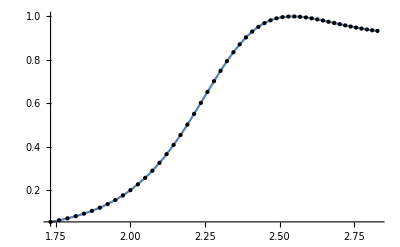

```mathematica
Plot[probTrasmBarriera[k,larghezza,β0],{k,kval[[1]],kval[[-1]]},PlotRange-> All,
Epilog-> Point/@probVsK]
```

## Evoluzione temporale

Possiamo seguire in dettaglio l' evoluzione temporale di un pacchetto risolvendo l’equazione di Schrödinger dipendente dal tempo.

Pacchetto d'onda iniziale: occorre trovare un compromeso fra la definizione in k e la larghezza, se il pacchetto è troppo largo occorre risolvere l’equazione su un intervallo troppo grande e si possono introdurre degli errori numerici.

Scegliamo un pacchetto centrato ad un impulso con energia minore di V0 per mostrare il tunneling

```mathematica
k0 = 0.9 β0;dk0 =  0.15*k0;
x0P = -25;
ψ0[x_]:= ⅇ^(ⅈ k0 x- dk0^2(x-x0P)^2);
```

L' equazione da risolvere, in un intervallo spaziale -L, L è

```mathematica
equation[L_] := {ⅈ D[u[x,t], t]==-1/2 D[u[x,t], x,x] + V[x]u[x,t] ,u[x,0]==ψ0[x],u[L,t]== 0,u[-L,t]== 0};
```

come si vede si sono imposte condizioni zero al bordo e u[x] = ψ0 al tempo t=0. Le condizioni nulle la bordo comporteranno un artificiale riflessione.

```mathematica
L=50;tmax = 30.;
```

```mathematica
ψ=u/.First[NDSolve[equation[L],u,{x,-L,L},{t,0,tmax},PrecisionGoal-> 7]];//Timing
```

{3.08207,Null}

```mathematica
Animate[Plot[Abs[ψ[x,t]]^2,{x,-L,L},Filling-> Axis,
PlotRange->{{-L,L},{0,1.1}},Epilog->{
Text[Style["t="<>ToString[t],FontSize-> 12],{-40,1}],
RGBColor[1,0,0],Rectangle[{aL,0},{aR,1}]}],{t,0,tmax},AnimationRepetitions->1,
AnimationRunning->False]
```

## Analisi di Fourier del risultato

Per linearità l’onda trasmessa deve essere l’integrale su k di f(k) T(k) Exp[ⅈ k x], mentre nell’onda riflessa deve comparire la componente di Fourier - k0 (impulso iniziale riflesso).

Nel caso di una gaussiana è possibile effettuare analiticamente la trasformta di Fourier, ma in generale si può usare una trasformata di Fourier discretizzata, calcolata con un algoritmo di Fast Fourier Transform, su una griglia di punti.

L’ordinamento dei k nella trasformata di Fourier di Mathematica è particolare.

Qui diamo una funzione che data una griglia spaiale su cui si effettua il campionamento della funzione, fornisce la griglia dei k che sono calcolati. L'input sono gli estremi dell'intervallo ed il numero di intervallini in cui si vuole suddividere il dominio. In uscita viene fornita la griglia nelle x e nei k

```mathematica
getGriglia[xLeft_,xRight_,ndx_]:=
Module[{Lbox,dx,xpt,k},
Lbox = xRight-xLeft; (* estensione dell'intervallo *)
dx = N[Lbox/(ndx+1)];   
xpt = N[Range[xLeft,xRight-dx,dx]]; 
k = N[Join[{0},2 π/Lbox Range[Ceiling[(Length[xpt]-1)/2]],-2 π/Lbox Range[Floor[(Length[xpt]-1)/2],1,-1]]];
{xpt,k}];
```

Nel problema in esame

```mathematica
xLeft = -50; xRight=+50; numIntervalli = 5000 ;
{xpt,k} = getGriglia[xLeft,xRight,numIntervalli];
```

Il massimo valore di k e la risoluzione della griglia in k sono dati evidentemente da

```mathematica
{Max[k],k[[3]]-k[[2]]}
```

{157.08,0.0628319}

Siccome nel pacchetto δk ∼ 0.27 la risoluzione è sufficiente.

Per passare da ψ[x] a f[k] con la convenzione della FFT rispetto a quella usata in questo corso occorre usare la funzione InverseFourier, sul vettore di valori di ψ sulla griglia.

Ad esempio per l'onda iniziale lo spettro è (la linea rossa è il valore di k0)

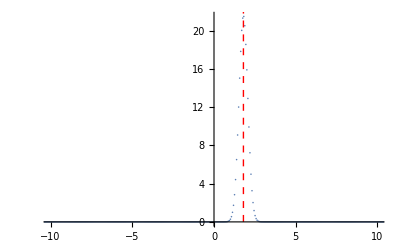

```mathematica
spettroIniz = Abs[InverseFourier[ψ0[xpt]]]^2;
ListPlot[Transpose[{k,spettroIniz}],PlotRange-> {{-10,10},All},
Epilog-> {Dashed,Red,Line[{{k0,0},{k0,50}}]}
]
```

Per l' onda dopo il processo d' urto consideriamo un t successivo all’urto ma inferiore al tempo in cui si incominciano a manifestare i riflessi al bordo. Dall’animazione precedente un tempo poco sopra 25 va bene.

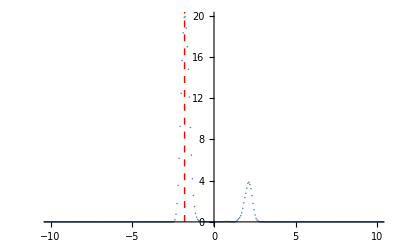

```mathematica
tOnda = 25.48;
spettro =  Abs[InverseFourier[ψ[xpt,tOnda]]]^2;
ListPlot[Transpose[{k,spettro}],PlotRange-> {{-10,10},All},
Epilog-> {Dashed,Red,Line[{{-k0,0},{-k0,100}}]}]
```

Si vede chiaramente un picco per valori positivi ed uno per valori negativi di k, questi corrispondono rispettivamente all'onda trasmessa e riflessa (impulso - k0, riportato in figura).

#### Onda trasmessa

Isoliamo l' onda trasmessa moltiplicando ψ per una funzione θ[x-aR], che è zero per x < aR (l'estremo destro della barriera). Verifichiamo che il nuovo spettro ha, come aspettato, un picco solo per k positivi

```mathematica
tOnda = 25.48;
```

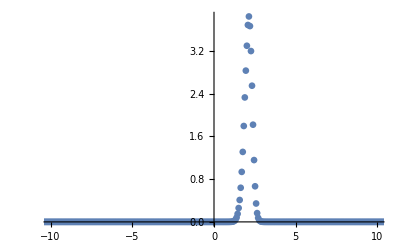

```mathematica
spettroTrasmesso =  Abs[InverseFourier[ψ[xpt,tOnda]UnitStep[xpt-aR]]]^2;
plotSpectrum=ListPlot[Transpose[{k,spettroTrasmesso}],PlotRange-> {{-10,10},All},PlotStyle-> PointSize-> 0.012]
```

Ci aspettiamo che lo spettro dell' onda trasmessa sia

|f[k]|^2 |T[k]|^2

```mathematica
fsp = Interpolation[Transpose[{k,spettroIniz}]];
```

Il confronto fra quanto aspettato (linea rossa) e quanto calcolato numericamente prima :

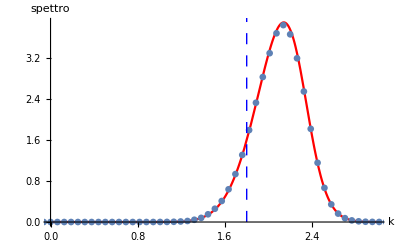

```mathematica
Show[Plot[probTrasmBarriera[kx,larghezza,β0]fsp[kx],{kx,0,3},
AxesLabel-> {"k","spettro"},PlotStyle-> Red,
Epilog->{Dashing[{0.02,0.02}],Blue,Line[{{k0,0},{k0,5}}]}],
plotSpectrum]
```

Chiaramente nell’onda trasmessa ci sono prevalentemente le componenti di Fourier del pacchetto iniziale con k>β0 (= 2) ma sono presenti anche componenti più basse in maniera rilevante.